# 1

## PHAS2443: Practical Mathematics II Lecture 1: Programming Styles

This lecture does not introduce many new concepts: it is intended mainly to remind you of some basic features of the Mathematica language which were covered in the PHAS1449 course. At the same time, it is intended to encourage you to think about the different ways of writing programs in Mathematica.

The programming styles that are supported straightforwardly by Mathematica are Rule-Based, Functional and Procedural (I say 'straighforwardly' because although Object-Oriented programming is not built in there are various add-on packages which implement it). In  most cases the functional approach produces the most efficient and readable code, but rules can offer neat ways of manipulating data structures. 

  In crude terms, the functional approach uses functions that act directly on data structures, whereas procedural programming tends to pick structures apart, act on the elements, and put them back together. Procedural methods usually contain explicit loops (Do, For, While etc.). Sometimes the choice of method can make a lot of difference. Consider, for example, adding the elements in a list:

```mathematica
ll=Table[RandomReal[],{i,1,10^6}];
Timing[sum=0;Do[sum=sum+ll⟦i⟧,{i,1,Length[ll]}];sum]
Timing[sum=∑_(i=1)^Length[ll] ll⟦i⟧]
Timing[sum=Plus@@ll]
Timing[Total[ll]]
Clear[ll]
```

{1.15713,500204.}

{0.456074,500204.}

{0.180823,500204.}

{0.002272,500204.}

Clearly, the slowest approach was the procedural one. Using the built-in function which is specially tailored to finding sums of expressions was almost twice as fast. It was considerably faster to use Apply (@@) to replace the Head of the expression (List) with Plus, but best of all was the built-in function Total. It is reassuring to note that all the answers are the same.

## Rule-Based Programming

Rule-based programming typically contains statements of the form
   expr/.rules
 expr //.rules
and rules may be immediate
  pattern→result
or delayed
  pattern:> result.
  As an example of the difference between an immediate and a delayed rule, consider

```mathematica
{x,x,x}/.x->RandomReal[]
{x,x,x}/.x:>RandomReal[]
```

{0.960995,0.960995,0.960995}

{0.738477,0.334325,0.602163}

The difference between ReplaceAll (/.) and ReplaceRepeated (//.) is illustrated by

```mathematica
{a,b,c,c,d,d,d}/.{x___,y_,y_,z___}->{x,y,z}
{a,b,c,c,d,d,d}//.{x___,y_,y_,z___}->{x,y,z}
```

{a,b,c,d,d,d}

{a,b,c,d}

### Getting the Pattern Right

Remember that rules are pattern-matching constructions. Sometimes a rule will not work as expected, and this is usually because the form in which Mathematica holds an expression is not quite what you expected. For example, you might try to define a complex conjugate rule as follows

```mathematica
ccrule=ⅈ->-ⅈ
```

ⅈ→-ⅈ

enjoy initial success

```mathematica
a+ⅈ b/.ccrule
```

a-ⅈ b

and then be disappointed

```mathematica
4+3ⅈ/.ccrule
```

4+3 ⅈ

To explain this, we need to see how Mathematica stored the complex numbers

```mathematica
FullForm[a+ⅈ b]
FullForm[4+3ⅈ]
```

Plus[a,Times[Complex[0,1],b]]

Complex[4,3]

The rule interpreter recognises the bare symbol ⅈ because

```mathematica
FullForm[ⅈ]
```

Complex[0,1]

but other complex numbers are stored in a different form. A general approach would be

```mathematica
ccrule=Complex[a_,b_]->Complex[a,-b]
a+ⅈ b/.ccrule
4+3ⅈ/.ccrule
```

Complex[a_,b_]→Complex[a,-b]

a-ⅈ b

4-3 ⅈ

### Selective Patterns

All the features of patterns can be used in rules: this can include specifying the type of object to be matched, applying logical tests (/;), testing conditions (_?), supplying default values (_. or _:val), allowing alternatives (||), and so on. Here are some examples to illustrate these features.

If we want to plot a line with a semicircular bump, we could use

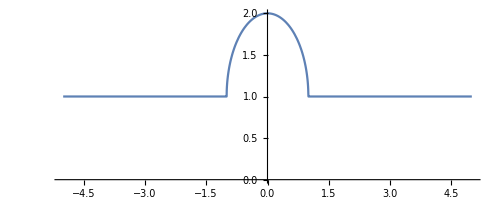

```mathematica
cc[x_/;-1≤x≤1]:=1+√(1-x^2)
cc[x_/;Abs[x]>1]:=1
Plot[cc[x],{x,-5,5},PlotRange->{All,{0,2}},AspectRatio->Automatic]
```

```mathematica
pyth[x_Integer?Positive,y_Integer?Positive,z_Integer?Positive]:=x^2+y^2==z^2
pyth[___]:=False
pyth[3,4,5]
pyth[-3,4,5]
pyth[3.,4.,5.]
```

True

False

False

```mathematica
tt=11 Sin[t]-2 Tan[2 t]+Sin[1+t]
Cases[tt,_ Sin[_]]
Cases[tt,_. Sin[_]]      (* _. represents an argument that can be omitted *)
```

11 Sin[t]+Sin[1+t]-2 Tan[2 t]

{11 Sin[t]}

{11 Sin[t],Sin[1+t]}

### Example: Bubble Sort

The bubble sort is a very basic sorting algorithm: given a list, it simply checks to see whether any element is larger than the one above it, and if so it swaps them over. This sorting scheme is simple, but not very efficient.

```mathematica
ll=Table[RandomReal[],{i,1,10}]
```

{0.223619,0.965395,0.24831,0.0659508,0.0441561,0.742433,0.823341,0.926241,0.554998,0.714687}

```mathematica
bsrule={a___,b_,c_,d___}/;(c>b)->{a,c,b,d}
```

{a___,b_,c_,d___}/;c>b→{a,c,b,d}

```mathematica
ll//.bsrule
```

{0.965395,0.926241,0.823341,0.742433,0.714687,0.554998,0.24831,0.223619,0.0659508,0.0441561}

## Functional Programming

Functions take one or more arguments and return a result (which may be a list, corresponding to several results). The arguments may themselves be functions, and functions may be nested, or indeed recursive. Ideally a function should depend only on its arguments, and it should produce its results without affecting the values of any global variables. All the variants of patterns may be used in defining the arguments to functions: functions may be defined for specific values of their arguments, and function definitions may be accumulated and will be used in a logical sequence, progressing from the most specific cases of their arguments to the most general. It is sometimes useful to remember values that have previously been calculated.

### Recursion and Saving Results

The Collatz problem iterates an integer as follows
c(n) = {3n+1  if n is odd
n/2       if n is even
and it seems (but has not been proved) that the sequence eventually settles into the sequence 1,4,2,1,4,... for any starting integer.

```mathematica
coll[n_?OddQ]:=3n+1
coll[n_?EvenQ]:=n/2
n=5;While[n≠1,n=coll[n];Print[n]];
```

16

8

4

2

1

Let's ask how long the sequence takes to reach 1 from a particular starting point.

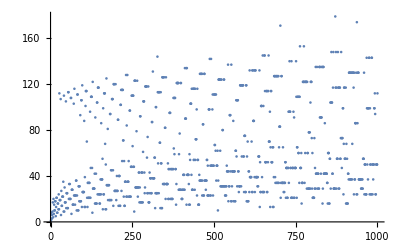

{0.266079,Null}

```mathematica
lencoll[n_]:=Module[{nw=n,len=1},While[nw≠1,nw=coll[nw];len=len+1];len]
Timing[Print[ListPlot[Table[lencoll[n],{n,1,1000}]]]]
```

Alternatively, we could adopt a recursive form of the function. Obviously the length of the sequence for n=1 is 1, and for any other number n the length is one greater than the length of the sequence for the number which follows n in the sequence.

```mathematica
lencollrec[1]=1;
lencollrec[n_]:=1+lencollrec[coll[n]]
```

```mathematica
Timing[Print[ListPlot[Table[lencollrec[n],{n,1,1000}]]]]
```

-Graphics-

{0.216402,Null}

That was a bit quicker. But in many cases a sequence will run into a result which has already been calculated. Let's try to economise by saving intermediate results.

```mathematica
lencollrecs[1]=1;
lencollrecs[n_]:=lencollrecs[n]=1+lencollrecs[coll[n]]
Timing[Print[ListPlot[Table[lencollrecs[n],{n,1,1000}]]]]
```

-Graphics-

{0.048697,Null}

```mathematica
Remove[lencollrecs]
```

### Pure Functions

If a function is just needed locally, for example to map onto a list once, it may be set up as a pure (unnamed) function. In a pure function, arguments are not given as named  patterns(such as x_) but as #n, denoting the nth argument. For example

```mathematica
{#1,#2,#1/#2}&[a,b]
```

{a,b,a/b}

does the same as

```mathematica
ff[a_,b_]:={a,b,a/b}
ff[a,b]
```

{a,b,a/b}

### Mapping

We often want to apply a function to each element of a list in turn. Map does this (remember that many of Mathematica's built-in functions have the Listable attribute, and automatically map themselves onto lists).

```mathematica
Map[ArcTan[#[[1]],#[[2]]]&,{{1,2},{2,3},{3,4}}]
```

{ArcTan[2],ArcTan[3/2],ArcTan[4/3]}

MapThread can be used with several lists

```mathematica
MapThread[ArcTan[#1,#2]&,{{1,2,3},{2,3,4}}]
```

{ArcTan[2],ArcTan[3/2],ArcTan[4/3]}

```mathematica
{ArcTan[2],ArcTan[3/2],ArcTan[4/3]}     (* Use of N here would force evaluation ! *)
```

{ArcTan[2],ArcTan[3/2],ArcTan[4/3]}

Like many of Mathematica's functions, although we usually think of it as applying to lists, Map is actually more general, and applies the mapped function to parts of the expression.

```mathematica
tt
Map[Log,tt]
Map[Log,tt,{2}]
Map[Log,tt,2]
```

11 Sin[t]+Sin[1+t]-2 Tan[2 t]

Log[11 Sin[t]]+Log[Sin[1+t]]+Log[-2 Tan[2 t]]

Log[11] Log[Sin[t]]+(ⅈ π+Log[2]) Log[Tan[2 t]]+Sin[Log[1+t]]

Log[Log[11] Log[Sin[t]]]+Log[(ⅈ π+Log[2]) Log[Tan[2 t]]]+Log[Sin[Log[1+t]]]

### Functional Forms of Loops

The functions Nest, NestList, Fold, FoldList, FixedPoint and FixedPointList allow us, for many applications, to avoid the use of Do and similar constructions. For example, to solve 
     f(x)=x
    we could pick an initial guess and iterate:

```mathematica
Nest[f,x0,4]
```

f[f[f[f[x0]]]]

```mathematica
NestList[f,x0,4]
```

{x0,f[x0],f[f[x0]],f[f[f[x0]]],f[f[f[f[x0]]]]}

```mathematica
NestList[Cos,3.1,25]   (*NB This returns initial value plus the req'd no of iterations *)
```

{3.1,-0.999135,0.54103,0.857179,0.654573,0.793308,0.701492,0.76388,0.722157,0.750382,0.731429,0.744221,0.735616,0.741418,0.737512,0.740144,0.738372,0.739566,0.738761,0.739303,0.738938,0.739184,0.739018,0.73913,0.739055,0.739106}

```mathematica
FixedPoint[Cos,3.1]
```

0.739085

Fold and FoldList can be used to accumulate values:

```mathematica
FoldList[f,0,{a,b,c,d}]          (* Fold would return the final element in the FoldList output *)
```

{0,f[0,a],f[f[0,a],b],f[f[f[0,a],b],c],f[f[f[f[0,a],b],c],d]}

```mathematica
FoldList[Plus,0,{a,b,c,d}]
```

{0,a,a+b,a+b+c,a+b+c+d}

```mathematica
{0,a,a+b,a+b+c,a+b+c+d}
```

{0,a,a+b,a+b+c,a+b+c+d}

## Procedural Programming

Do remember that it is usually much less efficient to program procedurally. As an example, compare these three ways of applying a function to each member of a list.

```mathematica
ff[x_]:=Log[1+x]
tt=Table[RandomReal[],{i,1,100000}];
Timing[Do[tt⟦i⟧=ff[tt⟦i⟧],{i,1,Length[tt]}]]
Timing[ff/@tt;]
SetAttributes[ff,Listable]         (* ff can be specifically made Listable *)
Timing[ff[tt];]
```

{0.365691,Null}

{0.112521,Null}

{0.129005,Null}

There are often cases where it is hard, or impossible, to see how to avoid Do, While, and similar constructions. An example might be the computation of the Mandelbrot set. This iterates a nonlinear function and evaluates the number of iterations before the magnitude of the result exceeds 2. Here is a function, defined with a default limit for the number of iterations. We'll evaluate this on a fairly coarse mesh (PlotPoints->10), but below here is pasted a result with PlotPoints->100.

```mathematica
mset[x_,y_,lim_:50]:=Module[{z0=x+I y,z=x + I y,steps=1},While[(Abs[z]<2)&&(steps<lim),z=z^2+z0;steps++];steps]
```

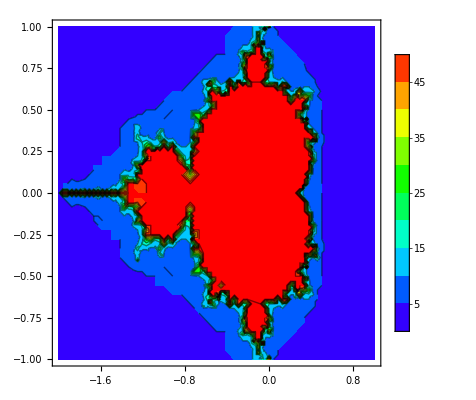

{0.474742,Null}

```mathematica
cf[h_]:=Hue[0.7*(1-h)]
Timing[Print[ContourPlot[mset[x,y],{x,-2,1},{y,-1,1},PlotPoints->10,Mesh->False,ColorFunction->cf,PlotLegends->Automatic]]]
```

Here' s the result with the finer mesh :
-Graphics-

Even in a case like this, where we do not know in advance how many iterations are going to be needed, we can avoid the While loop construction -- by using NestWhileList.

```mathematica
msetf[x_,y_,lim_:50]:=Length[NestWhileList[#^2+x+I y&,x+I y,Abs[#]<2&,1,lim]]-1
```

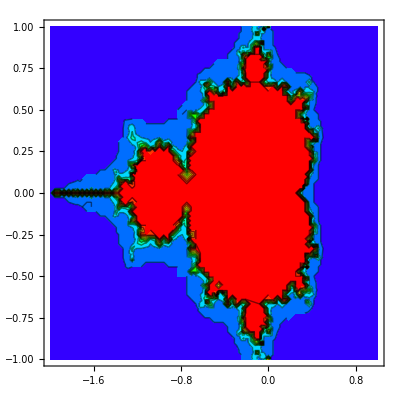

{0.329702,Null}

```mathematica
Timing[Print[ContourPlot[msetf[x,y],{x,-2,1},{y,-1,1},PlotPoints->10,Mesh->False,PlotRange->All,ColorFunction->cf]]]
```

So here again the functional approach is a bit more efficient than the procedural.

## Case Study: Newton's Method

Newton's method for finding the zero of a function is simple but often effective. Start by plotting the function

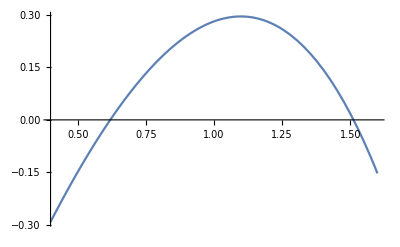

```mathematica
fn:=3x-Exp[x];p1=Plot[fn,{x,0.4,1.6}]
```

Estimate a value for the root, 0.8 say.

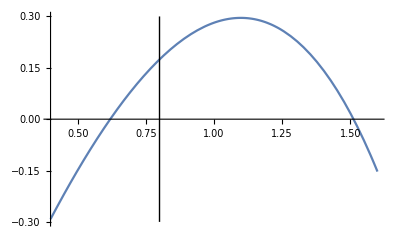

```mathematica
est=x->0.8;
Show[p1={p1,Graphics[Line[{{x,-0.3},{x,0.3}}/.est]]},PlotRange->All]
```

Now find the tangent at this guessed root, and see where it intersects the axis

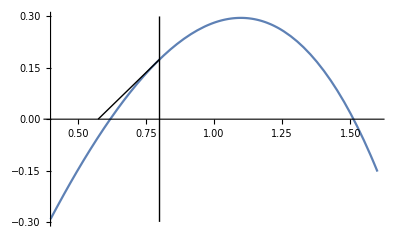

```mathematica
slope=D[fn,x]/.est;
Show[p1={p1,Graphics[Line[{{x,fn},{x-fn/slope,0.}}/.est]]},PlotRange->All]
```

This gives a new estimate of the root, from which we can repeat the calculation.

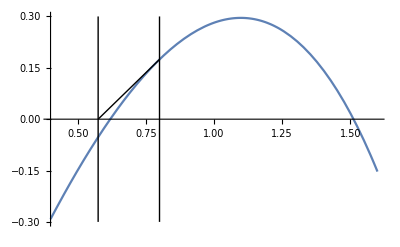

```mathematica
Show[{p1,Graphics[Line[{{x-fn/slope,-0.3},{x-fn/slope,0.3}}/.est]]},PlotRange->All]
```

Let's write a simple module to carry this iteration through to a specified level of accuracy, and get it to return the sequence of values it obtains.

```mathematica
newton[f_,x_,x0_,eps_:10^-10,max_:100]:=Module[{xi=x0,fi,df=D[f,x],dfi,iters={x0}},
Do[{fi,dfi}=N[{f,df}/.x->xi];
If[Abs[fi]<eps,Break[]];xi=xi-fi/dfi;iters={iters,xi},{max}];Flatten[iters]]
```

```mathematica
newton[fn,x,.8]
```

{0.8,0.574734,0.617613,0.61906,0.619061}

```mathematica
{0.8,0.5747342914223509,0.6176131701891086,0.619059588428839,0.6190612867336015}
```

{0.8,0.574734,0.617613,0.61906,0.619061}

```mathematica
fn/.x->Last[newton[fn,x,.8]]
```

-2.67852×10^-12

This has clearly worked. Let's look at a few features of the module.
   1. Note that we supplied default values for the accuracy and the maximum number of iterations.
   2. When accumulating values we used iters={iters,xi} rather than AppendTo[iters,xi]. This is because AppendTo is rather slower, even when we add in the time needed to Flatten the list at the end.
   3. As the statement iters={iters,xi} came right after the calculation of xi, we might have been tempted to use iters={iters,%}. This would not have worked -- we can only use % in interactive calculations, when in refers to the contents of the last Out[...] box.
   4. We have had to introduce the variable xi. This is because the arguments of a function cannot be changed inside that function, so we cannot use x0 as the working variable for the current best estimate of the root. The underlying reason for this is that when the function is called x0 has a numerical value, and attempting to use x0 as the working variable would have resulted in statements that evaluated to, for example, 0.8=0.574374, which are for good reasons invalid.
   5. In the declaration part of the module, we have used iters={x0}. It is important to note that we could not have written iters={xi}, despite the fact that we have defined xi=x0 in the declaration. We cannot use values defined within the declaration elsewhere in the declaration.

Can we rewrite our Newton's method code without the Do loop? The obvious function to try is FixedPointList, but how can we build in our stopping criterion (we do not necessarily want to iterate to machine precision) and our ability to exit after a given number of iterations (we may not want to go as far as Mathematica's built-in iteration limit)?

```mathematica
$IterationLimit
```

4096

We can use NestWhileList, as follows.

```mathematica
newton2[f_,x_,x0_,eps_:10^-10,max_:100]:=Module[{df=D[f,x]},Flatten[NestWhileList[#-N[(f/df)/.x->#]&,x0,Abs[f/.x->#]>eps&,1,max]]]
```

```mathematica
newton2[fn,x,.8]
```

{0.8,0.574734,0.617613,0.61906,0.619061}

```mathematica
fn/.x->Last[newton2[fn,x,.8]]
```

-2.67852×10^-12

## Summary

We have seen that in most cases a functional approach is more efficient than a procedural one.

A.H. Harker
Physics and Astronomy, UCL
September 2005, updated January 2009, January 2011,January 2016.